# Testing singleSlipPlaneSolution.yaml with Saturation Hardening

In this notebook, we examine slip along a plane that is rotated to the global axes.

<!-- =========================================================================================== -->

     <ParameterList name=”Materials”>

          <ParameterList name=”metal_fcc”>


<!-- ~~~~~~~~~ Specify material model ~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~ -->

               <ParameterList name=”Material Model”>

                    <Parameter name=”Model Name”
                               type=”string”
                               value=”CrystalPlasticity”/>

               </ParameterList>


<!-- ~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~ -->
<!-- ~~~~~~~~~ Set program controls ~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~ -->
<!-- ~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~ -->

               <Parameter name=”Integration Scheme”
                          type=”string”
                          value=”Implicit”/>

               <Parameter name=”Implicit Integration Relative Tolerance”
                          type=”double”
                          value=”1.0e-35”/>

               <Parameter name=”Implicit Integration Absolute Tolerance”
                          type=”double”
                          value=”1.0e-10”/>

               <Parameter name=”Implicit Integration Max Iterations”
                          type=”int”
                          value=”100”/>

       <ParameterList name=”Crystal Elasticity”>

                    <Parameter name=”C11”
                               type=”double”
                               value=”204.6e3”/>

                    <Parameter name=”C12”
                               type=”double”
                               value=”137.7e3”/>

                    <Parameter name=”C44”
                               type=”double”
                               value=”126.2e3”/>

                    <Parameter name=”Basis Vector 1”
                               type=”Array(double)”
                               value=”{-0.09175170953613698, | 0.908248290463863, | 0.408248290463863}”/>

                    <Parameter name=”Basis Vector 2”
                               type=”Array(double)”
                               value=”{0.908248290463863, | -0.09175170953613698, | 0.408248290463863}”/>

                    <Parameter name=”Basis Vector 3”
                               type=”Array(double)”
                               value=”{0.408248290463863, | 0.408248290463863, | -0.816496580927726}”/>

               </ParameterList>
               
        <!-- ~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~ -->
<!-- ~~~~~~~~~ Set crystal plasticity parameters ~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~ -->
<!-- ~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~ -->

               <Parameter name=”Number of Slip Systems”
                          type=”int”
                         value=”1”/>

<!-- ~~~~~~~~~ Specify slip system 1 ~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~ -->

               <ParameterList name=”Slip System 1”>

                    <Parameter name=”Slip Direction”
                               type=”Array(double)”
                               value=”{-1.0, 1.0, 0.0}”/>

                    <Parameter name=”Slip Normal”
                               type=”Array(double)”
                               value=”{1.0, 1.0, 1.0}”/>

                    <Parameter name=”Tau Critical”
                               type=”double”
                               value=”122.0”/>

                    <Parameter name=”Gamma Dot”
                               type=”double”
                               value=”1.0”/>

                    <Parameter name=”Gamma Exponent”
                               type=”double”
                               value=”50.0”/>

                    <Parameter name=”Hardening”
                               type=”double”
                               value=”0.0”/>

                    <Parameter name=”Hardening Exponent”
                               type=”double”
                               value=”0.0”/>

               </ParameterList>

## State basis for material coordinate system

Looking at a basis derived to simplify Schmid tensor and E3 (for debugging)

```mathematica
basis = {{1/Sqrt[6]-1/2,1/Sqrt[6]+1/2,1/Sqrt[6]},{1/Sqrt[6]+1/2,1/Sqrt[6]-1/2,1/Sqrt[6]},{1/Sqrt[6],1/Sqrt[6],-2/Sqrt[6]}};
MatrixForm[basis];
MatrixForm[N[basis,16]]
checkBasis = Norm[Simplify[basis . Transpose[basis]-IdentityMatrix[3]]];
checkDot12 = Simplify[basis[[1,All]] . basis[[2,All]]];
checkDot13 = Simplify[basis[[1,All]] . basis[[3,All]]];
checkDot23 = Simplify[basis[[2,All]] . basis[[3,All]]];
checkCross12= Norm[Simplify[Cross[basis[[1,All]],basis[[2,All]]]-basis[[3,All]]]];
checkCross23 = Norm[Simplify[Cross[basis[[2,All]],basis[[3,All]]]-basis[[1,All]]]];
checkCross31 = Norm[Simplify[Cross[basis[[3,All]],basis[[1,All]]]-basis[[2,All]]]];
checkDet=Det[basis]-1;
```

(-0.09175170953613698 | 0.908248290463863 | 0.408248290463863
0.908248290463863 | -0.09175170953613698 | 0.408248290463863
0.408248290463863 | 0.408248290463863 | -0.816496580927726)

## Derive direction cosine matrix for coordinate transformations

```mathematica
orientation = Transpose[basis];
MatrixForm[orientation]
```

(-1/2+1/(√6) | 1/2+1/(√6) | 1/(√6)
1/2+1/(√6) | -1/2+1/(√6) | 1/(√6)
1/(√6) | 1/(√6) | -√(2/3))

## Transform slip and normal directions to global coordinate system

```mathematica
slipdirectionGlobal = Simplify[orientation . {{-1/Sqrt[2]},{1/Sqrt[2]},{0}}];
slipnormalGlobal = Simplify[orientation . {{1/Sqrt[3]},{1/Sqrt[3]},{1/Sqrt[3]}}];
MatrixForm[slipdirectionGlobal];
MatrixForm[slipnormalGlobal];
```

## Create Schmid tensor

```mathematica
projection =Outer[Times,Transpose[slipdirectionGlobal][[1]],Transpose[slipnormalGlobal][[1]]];
symmProjection = 0.5 * (projection + Transpose[projection]);
projFactor = 2 * (Norm[symmProjection, "Frobenius"]^2);
MatrixForm[symmProjection]
Print[projFactor]
```

(0.5 | 0. | 0.
0. | -0.5 | 0.
0. | 0. | 0.)

1.

## Define velocity gradient Lp_{n+1}

```mathematica
Lpnplus1 = gammaDot*projection;
MatrixForm[Lpnplus1];
```

## Find Fp_{n+1} through the exponential map

This is the form of Fp.

```mathematica
Fpnplus1 = MatrixExp[Δt*Lpnplus1] . {{Fpn11,Fpn12,Fpn13},{Fpn21,Fpn22,Fpn23},{Fpn31,Fpn32,Fpn33}} /. {Δt*gammaDot -> γnp1 - γn};
MatrixForm[Fpnplus1];
```

## Impose uniaxial strain and find Fe_{nplus1} and Ee_{nplus1}

```mathematica
Fapplied = {{1+c*t,0,0},{0,1,0},{0,0,1}};
```

```mathematica
Fenplus1 = Simplify[Fapplied . Inverse[Fpnplus1]];
Cenplus1 = Simplify[Transpose[Fenplus1] . Fenplus1];
Id3 = {{1,0,0},{0,1,0},{0,0,1}};
Eenplus1 = Simplify[1/2*(Cenplus1 - Id3)];
MatrixForm[Eenplus1];
```

## Calculate and rotate the elasticity tensor

```mathematica
elasTensor = Table[i*j*k*l*0,{i,1,3},{j,1,3},{k,1,3},{l,1,3}];
Do[elasTensor[[i,i,i,i]] = c11;
Do[elasTensor[[i,i,j,j]] = c12;
elasTensor[[j,j,i,i]] = c12;
elasTensor[[i,j,i,j]] = c44;
elasTensor[[j,i,j,i]] = c44;
elasTensor[[i,j,j,i]] = c44;
elasTensor[[j,i,i,j]] = c44,
{j,i+1,3}],{i,1,3}]
MatrixForm[elasTensor];
```

```mathematica
transformElasTensor = Table[i*j*k*l*0,{i,1,3},{j,1,3},{k,1,3},{l,1,3}];
Do[ Do[transformElasTensor[[w,v,u,t]]= transformElasTensor[[w,v,u,t]] + elasTensor[[p,q,r,s]]*orientation[[p,w]]*
orientation[[q,v]]*orientation[[r,u]]*orientation[[s,t]],{s,1,3},{r,1,3},{q,1,3},{p,1,3}],{t,1,3},{u,1,3},{v,1,3},{w,1,3}];
MatrixForm[transformElasTensor];
```

## Get 2nd PK stress in the intermediate configuration

```mathematica
Snplus1 = Table[i*j*0,{i,1,3},{j,1,3}];
Do[
Do[Snplus1[[i,j]] = Snplus1[[i,j]] + transformElasTensor[[i,j,k,l]]*Eenplus1[[k,l]],
{l,1,3},{k,1,3}],{j,1,3},{i,1,3}]
MatrixForm[Snplus1];
```

## Form residuals as a function of material parameters and state

There are now two residuals
R - this is the standard, power law residual for slip
Rhard - this is a residual that reflects an ODE to evolve the hardening. We must solve both residuals to obtain an solution.
g - slip resistance that is obtained from the solution of the dislocation densities (hardening equation)

```mathematica
slipRate = (γnp1 - γn)/Δt ;
gs = gs0 * Abs[slipRate/ gammaDot0]^ω;
tau1 = Tr[Transpose[Cenplus1.Snplus1] . projection];
partR = Δt*gammaDot0*(Abs[tau1]/(gnp1))^k*signtau1;
partRhard =  Δt*g0Dot* (gs - gnp1) / (gs - g0) * projFactor * Abs[slipRate];
R = (γnp1 - γn) - partR; 
Rhard = (gnp1 - gn) - partRhard;

γinit = 0.0;
ginit = 90;
```

## Invoking scaling of the tangent

Scaling by the residual is not appropriate - we need to scale with the tangent. Scaling R by what is blowing up, (Abs[tau1]/tau0)^k, will be infinity for tau1 = 0. Diagonal scaling via the tangent does not suffer this issue. I can put together a residual with a Piecewise statement, but preliminary findings indicate that this is not helpful. You have just moved the problem from a part of the residual that blows up to a part of the residual that goes to zero. Scaling the tangent is more helpful.

```mathematica
RScaled = Piecewise[{{R/(Abs[tau1]/tau0)^k,γnp1!= 0},{R,γnp1 ==0}}];
RScaledhard = Rhard;
```

## Incorporating material parameters and state

```mathematica
parameters = {c11 -> 204600, c12 -> 137700, c44 -> 126200,c -> 1,gammaDot0 -> 1*10^(-3), k -> 20 ,ω -> 0.01, g0 -> 90, gs0 -> 202, g0Dot -> 20000};
state = {Fpn11 -> 1, Fpn12 -> 0, Fpn13 -> 0, Fpn21 -> 0, Fpn22 -> 1, Fpn23 -> 0, Fpn31 -> 0, Fpn32 -> 0, Fpn33 -> 1, γn -> 0.0, gn -> 0.0};
Rparam = R /. parameters;
RScaledparam = RScaled /. parameters;
tau1param =tau1 /. parameters;
Rhardparam = Rhard /. parameters;
RScaledhardparam = RScaledhard /. parameters;
Reval = Rparam /. {signtau1 -> Sign[tau1param]} /. state;
Rhardeval = Rhardparam /. state;
```

## Constructing the tangent

```mathematica
Element[{Fpn11, Fpn12,Fpn13,Fpn21, Fpn22, Fpn23, Fpn31, Fpn32, Fpn33},Reals];
Element[{γn,γnp1, gn, gnp1},Reals];
Element[{Δt ,t},Reals];
tangent ={{D[Rparam,γnp1], D[Rparam,gnp1]},{D[Rhardparam,γnp1],D[Rhardparam,gnp1]}};
(*tangentScaled ={{D[RScaledparam,γnp1], D[RScaledparam,gnp1]},{D[RScaledhardparam,γnp1],D[RScaledhardparam,gnp1]}};*)
```

```mathematica
tangentEval = tangent  /. {signtau1 -> Sign[tau1param]}/. state /. parameters /.{Δt -> 0.1,t -> 0}/. {γnp1-> γinit, gnp1 -> ginit};
(*tangentScaledEval = tangentScaled /. {signtau1 -> Sign[tau1param]}/. state /. {Δt -> 0, t -> 0}/. {γnp1-> γinit, gnp1 -> ginit, γn -> 0};*)
```

## Switching between residuals and scaled residuals - brute force copy

```mathematica
(*Rparam = RScaledparam;
Rhardparam = RScaledhardparam;*)
```

## Loop through time to construct a solution

```mathematica
(********************************************************************************************************)
(************************************ INITIALIZE VARIABLES/PARAMETERS ************************************)
(********************************************************************************************************)
(* time parameters *)
iloop = 1;
tn = 0;
finalTime = 0.005;
numberSteps = 10;
times = Table[i*0,{i,1,numberSteps+1}];

(* Set up parameters for Newton *)
absoluteTolerance = 1*10^-12;
maxIterations = 300;
timeIncrement = finalTime/numberSteps;

(*set up residual parameters *)
initialResidualsNewton = residualsNewton = Table[i*0,{i,1,numberSteps+1},{j,1,2}];
residualsNewton = Table[i*0,{i,1,numberSteps+1},{j,1,2}];
iterationsNewton = Table[i*0,{i,1,numberSteps+1}];
iterationResids = Table[0*i*j*k,{i,1,numberSteps+1},{j,1,maxIterations+1},{k,1,2}];

(*set up slip parameters*)
slips = Table[i*0,{i,1,numberSteps+1}];
slipsNewton = Table[i*0,{i,1,numberSteps+1}];
slipRateNewton = Table[i*0,{i,1,numberSteps+1}];

(*set up hardness parameters*)
hardNewton = Table[i*0,{i,1,numberSteps+1}];
hardRateNewton = Table[i*0,{i,1,numberSteps+1}];
taus = Table[i*0,{i,1,numberSteps + 1}];

(*set up tangent-scaling parameters*)
conditionNumber = Table[i*j*0,{i,1,numberSteps + 1},{j,1,maxIterations+1}];
scaledconditionNumber =  Table[i*j*0,{i,1,numberSteps + 1},{j,1,maxIterations+1}];

(*set up kinematic/constitutive/state parameters*)
axialStress = Table[i*0,{i,1,numberSteps +1}];
cauchy=Table[i*j*k*0,{k,1, numberSteps + 1},{i,1,3},{j,1,3}];
FOut = Table[i*j*k*0,{k,1, numberSteps + 1},{i,1,3},{j,1,3}];
FpOut = Table[i*j*k*0,{k,1, numberSteps + 1},{i,1,3},{j,1,3}];
state = {
Fpn11 -> 1, Fpn12 -> 0, Fpn13 -> 0,
 Fpn21 -> 0, Fpn22 -> 1, Fpn23 -> 0, 
Fpn31 -> 0, Fpn32 -> 0, Fpn33 -> 1,
 γn -> 0, gn -> ginit};
stateOld ={
Fpn11 -> 1, Fpn12 -> 0, Fpn13 -> 0,
 Fpn21 -> 0, Fpn22 -> 1, Fpn23 -> 0, 
Fpn31 -> 0, Fpn32 -> 0, Fpn33 -> 1,
 γn -> 0, gn -> ginit};

(********************************************************************************************************)
(***************************************** SET INITIAL VALUES  ******************************************)
(********************************************************************************************************)

(*set initial condition of dislocation density as first solution for hardness *)
hardNewton[[1]] = ginit;
slipsNewton[[1]] = γinit;
 
(* Initialize output for t = 0. Everything besides tangent, F, and Fp is zero*)
tangentEval = tangent  /. {signtau1 -> Sign[tau1param]}/. state /. {Δt -> timeIncrement, t -> 0}/. {γnp1->γinit, gnp1 -> ginit};

(* Calculate eigenvalues and condition number of tangent matrix, before preconditioning *)
eigsTangent = Eigenvalues[tangentEval];
conditionNumber[[iloop]] = Max[eigsTangent]/Min[eigsTangent];

(*Update elastic and plastic deformation gradients*)
FOut[[iloop,All,All]] = Fapplied /. parameters /. {t -> 0};
(*γnp1 is changed to non-zero initial guess; this prevents initial hardness residual from being zero*)
FpOut[[iloop,All,All]] = (Fpnplus1 /. state) /. γnp1-> γinit;

(* Increment time *)
iloop = iloop + 1;
tnplus1 = timeIncrement;.

(********************************************************************************************************)
(**************************************** START TIME LOOP ***********************************************)
(********************************************************************************************************)
While[tnplus1 ≤ finalTime,

(* Increment time *)
times[[iloop]] = tnplus1;

(* Residuals for both slip and hardening. Keep signtau *)
Reval = Rparam /.  {signtau1 -> Sign[tau1param]}/. state;
Rhardeval = Rhardparam /. state;

(* In Albany, we use a secant initial guess *)
slipsNewton[[iloop]] = slipsNewton[[iloop-1]] + slipRateNewton[[iloop-1]]*timeIncrement;
hardNewton[[iloop]] = 
hardNewton[[iloop-1]] + hardRateNewton[[iloop-1]]*timeIncrement;

(* Evaluate initial residual - prepare for N-R loop *)
RNewton = {{Reval},{Rhardeval}} 
/. {Δt -> timeIncrement, t -> tnplus1, γnp1 -> slipsNewton[[iloop]],gnp1 -> hardNewton[[iloop]]};

initialResidualsNewton[[iloop,1]] = RNewton[[1,1]];
initialResidualsNewton[[iloop,2]] = RNewton[[2,1]];

iterN = 1;

(********************************************************************************************************)
(**************************************** START NEWTON ITERATIONS ***************************************)
(********************************************************************************************************)

While[Norm[RNewton] > absoluteTolerance && iterN < maxIterations,

(* evaluate tangent at current state *)
tangentEval = FunctionExpand[tangent
/.  {signtau1 -> Sign[tau1param]}
/. state 
/. {Δt -> timeIncrement, t -> tnplus1}
/. {γnp1 -> slipsNewton[[iloop]],gnp1 -> hardNewton[[iloop]]}];

(* calculate eigenvalues and l2-norm condition number *)
eigsTangent = Eigenvalues[tangentEval];
cnTangent = Max[Abs[eigsTangent]]/Min[Abs[eigsTangent]];
conditionNumber[[iloop,iterN]] = cnTangent;

(* compute tangent scaling coefficients matrix *)
ScaleEqsMatrix = {{1,0},{0,1}};
ScaleVarsMatrix = {{1,0},{0,1}};

(* scale tangent and residual, and compute new condition number *)
scaledTangent = Inverse[ScaleVarsMatrix].ScaleEqsMatrix . tangentEval.ScaleVarsMatrix;
eigsScaledTangent = Eigenvalues[scaledTangent];
scaledconditionNumber[[iloop,iterN]]  = Abs[eigsScaledTangent[[1]]]/Abs[eigsScaledTangent[[2]]];
scaledResidual = ScaleEqsMatrix . RNewton;

invTang  = 1/(tangentEval[[1,1]]*tangentEval[[2,2]] - tangentEval[[1,2]]*tangentEval[[2,1]])*
{{tangentEval[[2,2]],-tangentEval[[1,2]]},{-tangentEval[[2,1]],tangentEval[[1,1]]}};

(* update solution*)
incr= -invTang. scaledResidual;

Print[RNewton];
Print[MatrixForm[tangentEval]];
slipIncr = slipsNewton[[iloop]]-slipsNewton[[iloop-1]];
If[slipIncr<0,Print["NO!!!! (well maybe?)"]; ];
If[Abs[slipIncr]>1.0,Print["Slip Increment is too large!",Abs[slipIncr]]; ];

slipsNewton[[iloop]]+=incr[[1,1]];
hardNewton[[iloop]] += incr[[2,1]];

RNewton = {{Reval},{Rhardeval}} 
/. {Δt -> timeIncrement, t -> tnplus1, γnp1 -> slipsNewton[[iloop]],gnp1 -> hardNewton[[iloop]]};

iterN++;
iterationResids[[iloop,iterN,1]] = {slipsNewton[[iloop]],RNewton[[1,1]]};
iterationResids[[iloop,iterN,2]] = {hardNewton[[iloop]],RNewton[[2,1]]};

];

(********************************************************************************************************)
(****************************************** END NEWTON ITERATIONS ***************************************)
(********************************************************************************************************)

Print[RNewton];
Print[iterN];

residualsNewton[[iloop,1]] = RNewton[[1,1]];
residualsNewton[[iloop,2]] = RNewton[[2,1]];
iterationsNewton[[iloop]] = iterN;

(* Get shear stress for post processing *)
tau1eval = tau1param  /. state;
tau1evalTime = tau1eval /. {Δt -> timeIncrement, t -> tnplus1};
taus[[iloop]] = tau1evalTime /.{γnp1 -> slipsNewton[[iloop]],gnp1 -> hardNewton[[iloop]]};

(* Get F for post processing *)
FOut[[iloop,All,All]] = Fapplied /. parameters /. {t -> tnplus1};

(* Get stresses for post processing *)
Fenplus1Eval = Fenplus1 /. parameters /. state  
/. {Δt -> timeIncrement, t -> tnplus1, γnp1 -> slipsNewton[[iloop]]};

Snplus1Eval = Snplus1 /. parameters /. state 
/. {Δt -> timeIncrement, t -> tnplus1, γnp1 -> slipsNewton[[iloop]]};

cauchy[[iloop,All,All]]=1/Det[Fenplus1Eval]* Fenplus1Eval .  Snplus1Eval . Transpose[Fenplus1Eval];
axialStress[[iloop]] = cauchy[[iloop,1,1]];

(* Get ready for next step and save Fpnplus1 *)
Fpnplus1Eval = (Fpnplus1 /. state) /. γnp1 -> slipsNewton[[iloop]];
FpOut[[iloop,All,All]] = Fpnplus1Eval;
stateOld = state;
state = {
Fpn11 -> Fpnplus1Eval[[1,1]], Fpn12 ->  Fpnplus1Eval[[1,2]], Fpn13 ->  Fpnplus1Eval[[1,3]],
Fpn21 ->  Fpnplus1Eval[[2,1]], Fpn22 ->  Fpnplus1Eval[[2,2]], Fpn23 ->  Fpnplus1Eval[[2,3]], 
Fpn31 ->  Fpnplus1Eval[[3,1]], Fpn32 ->  Fpnplus1Eval[[3,2]], Fpn33 ->  Fpnplus1Eval[[3,3]],
γn -> slipsNewton[[iloop]],gn -> hardNewton[[iloop]]
};
 
slipRateNewton[[iloop]] = (slipsNewton[[iloop]] - slipsNewton[[iloop-1]])/timeIncrement;
hardRateNewton[[iloop]] = (hardNewton[[iloop]] - hardNewton[[iloop-1]])/timeIncrement;

iloop = iloop + 1;
tnplus1 = tnplus1 + timeIncrement 
]
(********************************************************************************************************)
(****************************************** END TIME LOOP ***********************************************)
(********************************************************************************************************)
```

{{-6.12173×10^-16},{0.}}

1

{{-6.72325×10^-10},{0.}}

(1.00001 | 1.49406×10^-10
0. | 1.)

{{-5.80107×10^-20},{-0.0000134463}}

(1.00001 | 1.49404×10^-10
-20000. | 1.)

{{-1.50454×10^-21},{-5.40257×10^-15}}

3

{{-2.3407×10^-6},{1.81948×10^-12}}

(1.03124 | 5.20305×10^-7
-20000. | 1.)

{{-1.80075×10^-9},{0.0000175522}}

(1.03006 | 4.99658×10^-7
-19992.3 | 1.00039)

{{-7.94912×10^-16},{5.02719×10^-12}}

(1.03006 | 4.99645×10^-7
-19992.3 | 1.00039)

{{2.71051×10^-19},{5.59969×10^-15}}

4

{{-0.000722257},{0.0000175851}}

(8.26884 | 0.000160841
-19984.6 | 1.00039)

{{-0.000224063},{0.0128804}}

(3.99619 | 0.0000633229
-19783.2 | 1.01067)

{{-0.0000458654},{0.00565367}}

(2.63136 | 0.000033408
-19653. | 1.01756)

{{-3.01172×10^-6},{0.000590503}}

(2.33617 | 0.0000270811
-19611.4 | 1.0198)

{{-1.48049×10^-8},{3.31025×10^-6}}

(2.31623 | 0.0000266562
-19608.3 | 1.01996)

{{-3.60803×10^-13},{8.13549×10^-11}}

(2.31613 | 0.0000266541
-19608.3 | 1.01997)

{{-4.39102×10^-18},{-2.22045×10^-15}}

7

{{-0.00287552},{0.0482228}}

(27.6777 | 0.000632141
-19223.7 | 1.01997)

{{-0.00097085},{0.015296}}

(11.7365 | 0.000242685
-19018.9 | 1.0316)

{{-0.000274927},{0.0102169}}

(6.02824 | 0.000109274
-18851.4 | 1.04107)

{{-0.0000462556},{0.00328272}}

(4.24438 | 0.0000689228
-18757.5 | 1.04649)

{{-1.99431×10^-6},{0.000195448}}

(3.91224 | 0.000061521
-18734.7 | 1.04782)

{{-4.10784×10^-9},{4.31559×10^-7}}

(3.89745 | 0.0000611924
-18733.7 | 1.04788)

{{-1.71164×10^-14},{1.84297×10^-12}}

(3.89742 | 0.0000611918
-18733.7 | 1.04788)

{{-5.56738×10^-17},{-5.32907×10^-15}}

8

{{-0.000346908},{0.26883}}

(6.70066 | 0.000124791
-17853.2 | 1.04788)

{{-0.0000600486},{0.00308567}}

(4.61979 | 0.0000773864
-17783.8 | 1.0546)

{{-2.89725×10^-6},{0.000262707}}

(4.21256 | 0.000068256
-17758.5 | 1.05619)

{{-7.57418×10^-9},{7.40086×10^-7}}

(4.19217 | 0.0000678005
-17757.2 | 1.05628)

{{-5.18618×10^-14},{5.09903×10^-12}}

(4.19212 | 0.0000677993
-17757.2 | 1.05628)

{{-1.52981×10^-16},{-5.32907×10^-15}}

6

{{-0.0000567812},{0.352715}}

(4.47757 | 0.0000742247
-16777.1 | 1.05628)

{{-1.97711×10^-6},{-0.000252354}}

(4.15472 | 0.0000669862
-16795.7 | 1.05853)

{{-3.37581×10^-9},{3.53848×10^-7}}

(4.1416 | 0.0000666932
-16794.8 | 1.05859)

{{-1.0202×10^-14},{1.00098×10^-12}}

(4.14158 | 0.0000666927
-16794.8 | 1.05859)

{{-2.90241×10^-16},{-5.32907×10^-15}}

5

{{-0.000015006},{0.361429}}

(4.09834 | 0.0000657391
-15830.8 | 1.05859)

{{-5.69111×10^-8},{-0.000271442}}

(4.04618 | 0.0000645679
-15868.3 | 1.05974)

{{-3.17376×10^-12},{4.67907×10^-10}}

(4.0458 | 0.0000645593
-15868.3 | 1.05975)

{{-4.63659×10^-16},{1.77636×10^-15}}

4

{{-7.88797×10^-6},{0.354749}}

(3.96328 | 0.0000627162
-14940.7 | 1.05975)

{{-6.61318×10^-10},{-0.000237406}}

(3.95518 | 0.000062529
-14981.2 | 1.06068)

{{-1.97008×10^-14},{-8.04388×10^-11}}

(3.95515 | 0.0000625284
-14981.2 | 1.06068)

{{1.13299×10^-17},{-5.32907×10^-15}}

4

{{-6.48409×10^-6},{0.345069}}

(3.87648 | 0.0000607609
-14093. | 1.06068)

{{7.78429×10^-10},{-0.000223674}}

(3.87592 | 0.0000607424
-14133.7 | 1.06155)

{{-8.56704×10^-15},{-7.89626×10^-11}}

(3.87591 | 0.000060742
-14133.6 | 1.06155)

{{-5.69315×10^-16},{-1.77636×10^-15}}

4

Null.Null

## Sampling residual to confirm character

```mathematica
slipsSample = slipsNewton[[iloop-1]];
hardSample = hardNewton[[iloop-1]];
n = 1000;
samplingslipPoints = Range[slipsSample*0.98,slipsSample*1.1,slipsSample/n];
samplinghardPoints = Range[hardSample*0.98,hardSample*1.1,hardSample/n];
count =0;
m = Dimensions[samplinghardPoints][[1]];
residSample  =Table[0*i*j,{i,1,m^2},{j,1,3}];
Do[
count++;
residSample[[count,1]] = samplingslipPoints[[i]];
residSample[[count,2]] = samplinghardPoints[[j]];
residSample[[count,3]] = Norm[{Reval,Rhardeval}]^2 /. {Δt -> timeIncrement, t -> finalTime,gnp1-> samplinghardPoints[[j]], γnp1 -> samplingslipPoints[[i]]};,
{j,1,m},{i,1,m}];
(*ListLinePlot[Transpose[{samplingPoints,residSample}], PlotRange -> All]*)
ListPointPlot3D[residSample]
Print[slipsNewton[[iloop-1]],",",hardNewton[[iloop-1]]];
```

-Graphics3D-

0.00229296,127.572

# Residual Iterations Plots

```mathematica
Tplot =2;
ResidPlotListSlips =iterationResids[[Tplot,All,1]][[2;;iterationsNewton[[Tplot]],2]];
ResidPlotListHardness =iterationResids[[Tplot,All,2]][[2;;iterationsNewton[[Tplot]],2]];
ListLogPlot[{Abs[ResidPlotListSlips],Abs[ResidPlotListHardness]}, PlotRange->All]
iterationResids[[Tplot,All,1]];
```

ListLogPlot::argx: ListLogPlot called with 0 arguments; 1 argument is expected.

General::stop: Further output of ListLogPlot::argx will be suppressed during this calculation.

ListLogPlot[{{},{}},PlotRange→All]

## Plotting results for sanity check

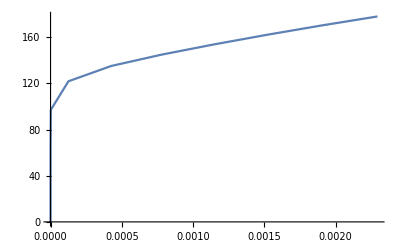

```mathematica
ListLinePlot[Transpose[{slipsNewton,taus}]]
```

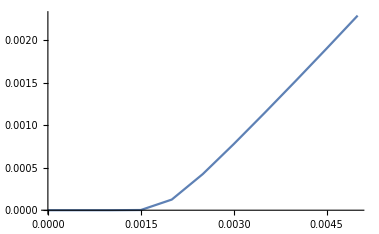

```mathematica
ListLinePlot[Transpose[{times,slipsNewton}]]
```

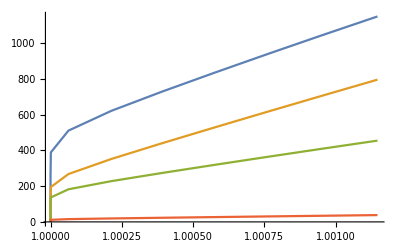

(1149.643028 | 38.02242151 | -161.0310713
38.02242151 | 795.9590155 | 6.031124012
-161.0310713 | 6.031124012 | 454.8209282)

```mathematica
ListLinePlot[{Transpose[{FpOut[[All,1,1]],cauchy[[All,1,1]]}],
Transpose[{FpOut[[All,1,1]],cauchy[[All,2,2]]}],
Transpose[{FpOut[[All,1,1]], cauchy[[All,3,3]]}],
Transpose[{FpOut[[All,1,1]], cauchy[[All,1,2]]}]}]
Print[NumberForm[MatrixForm[cauchy[[11,All,All]]],10]];
```

## Checking the hardening residual via an analytical solution

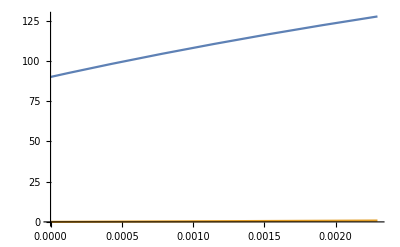

```mathematica
analyticalHard = H/Rd*(1 - Exp[-Rd*Abs[slipsNewton]])/. {H -> 355, Rd -> 2.9};
ListLinePlot[{Transpose[{slipsNewton,hardNewton}],Transpose[{slipsNewton,analyticalHard}]}]
```

```mathematica
(*iterPlot = (Take[iterationResids[[11]],iterationsNewton[[11]]])
iterLog10Plot = iterPlot;
Do[iterLog10Plot[[i,2]] = Log10[iterPlot[[i,2]]],{i,1,iterationsNewton[[11]]}];
ListLinePlot[iterPlot,PlotRange-> All]*)
```

```mathematica
initialResidualsNewton
residualsNewton
```

{{0,0},{-6.12173×10^-16,0.},{-6.72325×10^-10,0.},{-2.3407×10^-6,1.81948×10^-12},{-0.000722257,0.0000175851},{-0.00287552,0.0482228},{-0.000346908,0.26883},{-0.0000567812,0.352715},{-0.000015006,0.361429},{-7.88797×10^-6,0.354749},{-6.48409×10^-6,0.345069}}

{{0,0},{-6.12173×10^-16,0.},{-1.50454×10^-21,-5.40257×10^-15},{2.71051×10^-19,5.59969×10^-15},{-4.39102×10^-18,-2.22045×10^-15},{-5.56738×10^-17,-5.32907×10^-15},{-1.52981×10^-16,-5.32907×10^-15},{-2.90241×10^-16,-5.32907×10^-15},{-4.63659×10^-16,1.77636×10^-15},{1.13299×10^-17,-5.32907×10^-15},{-5.69315×10^-16,-1.77636×10^-15}}

```mathematica
iterationsNewton
Print[slipsNewton]
Print[hardNewton]
```

{0,1,3,4,7,8,6,5,4,4,4}

{0.,0.,6.72314×10^-10,2.2502×10^-6,0.000125473,0.000425542,0.000779258,0.00114777,0.00152366,0.00190551,0.00229296}

{90,90.,90.,90.045,92.4603,98.0751,104.342,110.511,116.448,122.135,127.572}

## Plotting the condition number per iteration for each time step

```mathematica
(* This plot shows a stable scaled condition number, and a linearly decreasing un-scaled condition number. *)
cNPlots = Table[Null,{i,1,numberSteps-1}];
Do[cNPlots[[i]] = ListPlot[Log10[conditionNumber[[i+1]]],PlotStyle->{Red}],{i,1,numberSteps-1}]
cNScaledPlots = Table[Null,{i,1,numberSteps-1}];
Do[cNScaledPlots[[i]] = ListPlot[Log10[scaledconditionNumber[[i+1]]],PlotStyle->{Blue}],{i,1,numberSteps-1}]
```

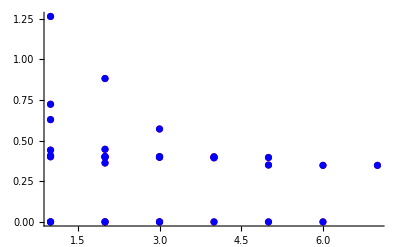

```mathematica
Show[{cNPlots,cNScaledPlots},PlotRange -> All]
```